#### Setting paths

```mathematica
$Here:=Quiet@Check[NotebookDirectory[],DirectoryName[$InputFileName]]; (*Folder that contains this notebook*)

(*locations*)
MatricesPath[]:=FileNameJoin[{$Here,"data","matrices"}];
PhiNumPath[]:=FileNameJoin[{$Here,"Phi_compute"}];
ResultsPath[]:=FileNameJoin[{$Here,"data","results"}];
FiguresPath[]:=FileNameJoin[{$Here,"data","figures"}];
```

#### Numerical parameters

```mathematica
NN=3;ν0=-20;
```

```mathematica
zν[ν_]=(√(4-ν0)-√(4-ν))/(√(4-ν0)+√(4-ν));(*mapping to unit circle*)
```

```mathematica
p=100;(*precision for numerical evaluation*)
M=100;(*number of points on the physical line*)
Δϕ=π/M;vϕ=Table[N[(i-1/2)Δϕ,p],{i,1,M}];νϕ[ϕ_]=ν0+(8-2 ν0)/(1+Cos[ϕ]);vx=νϕ[vϕ];(*set of points on the physical line*)
dxϕ[ϕ_]=D[νϕ[ϕ],ϕ];vdxϕ=dxϕ[vϕ];
ϕν[ν_]=ArcCos[(8-ν-ν0)/(ν-ν0)];
lmax=21;(*maximal spin*)nlmax=(lmax+1)/2;(*# of spins per isospin*)
nmax=50;(*# of coefficients*)
```

```mathematica
unit=SetPrecision[140,p];
```

pion mass as energy unit

```mathematica
s0h=(2 1000/unit)^2
```

204.081632653061224489795918367346938775510204081632653061224489795918367346938775510204081632653061

the high energy region is above s0h

```mathematica
n0=Length[Select[vx,#≤(2000/unit)^2&]]
```

79

number of points below s_0

#### Quick plots of form factor and spectral density

```mathematica
nWatson=25;
```

```mathematica
Ndata=IntegerString[#,10,2]&/@Range[1,nWatson]
```

{01,02,03,04,05,06,07,08,09,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

number of Watson iterations

```mathematica
Nclist=Table[IntegerString[i,10,2],{i,Range[3,12]}]
```

{03,04,05,06,07,08,09,10,11,12}

list of N_c

```mathematica
noshapeWNc=Table[Import[FileNameJoin[{ResultsPath[],"gtb_qcd_Nc"<>Nclist[[Nci]]<>"_W"<>IntegerString[i,10,2]<>".json"}],"RawJSON"],{Nci,1,Length[Nclist]},{i,1,Length[Ndata]}];
```

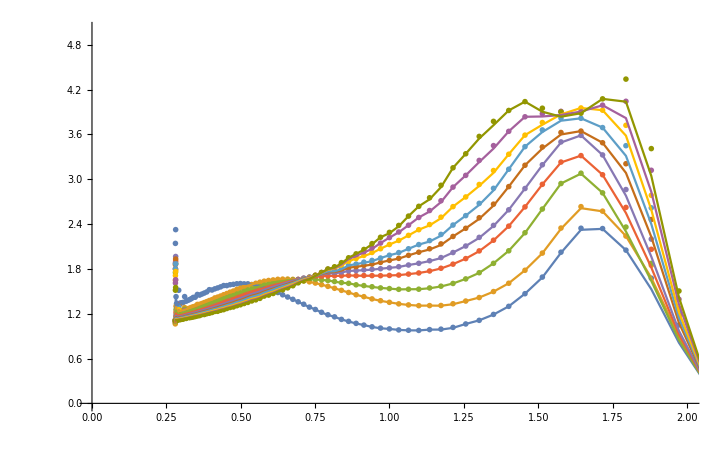

```mathematica
Show[{ListPlot[Table[Thread[{√vx[[1;;M]] unit/1000,√(noshapeWNc[[Nci,Length[Ndata]]]["specS0"][[1;;M]])}],{Nci,1,Length[Nclist]}],PlotRange->All],ListLinePlot[Table[Thread[{√vx[[1;;M]] unit/1000,Abs[noshapeWNc[[Nci,Length[Ndata]]]["ReFFS0"]+ⅈ noshapeWNc[[Nci,Length[Ndata]]]["ImFFS0"]][[1;;M]]}],{Nci,1,Length[Nclist]}],PlotRange->All]},GridLines->{{4 140/1000,0.77},None},PlotRange->{{0,2},{0,5}}]
```

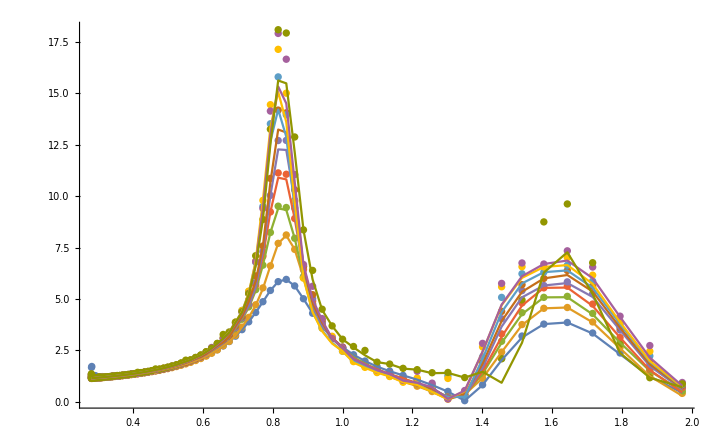

```mathematica
Show[{ListPlot[Table[Thread[{√vx[[1;;n0]] unit/1000,√(noshapeWNc[[Nci,Length[Ndata]]]["specP1"][[1;;n0]])}],{Nci,1,Length[Nclist]}],PlotRange->All],ListLinePlot[Table[Thread[{√vx[[1;;n0]] unit/1000,Abs[noshapeWNc[[Nci,Length[Ndata]]]["ReFFP1"]+ⅈ noshapeWNc[[Nci,Length[Ndata]]]["ImFFP1"]][[1;;n0]]}],{Nci,1,Length[Nclist]}],PlotRange->All]},GridLines->{{4 140/1000,0.86},None},PlotRange->All]
```

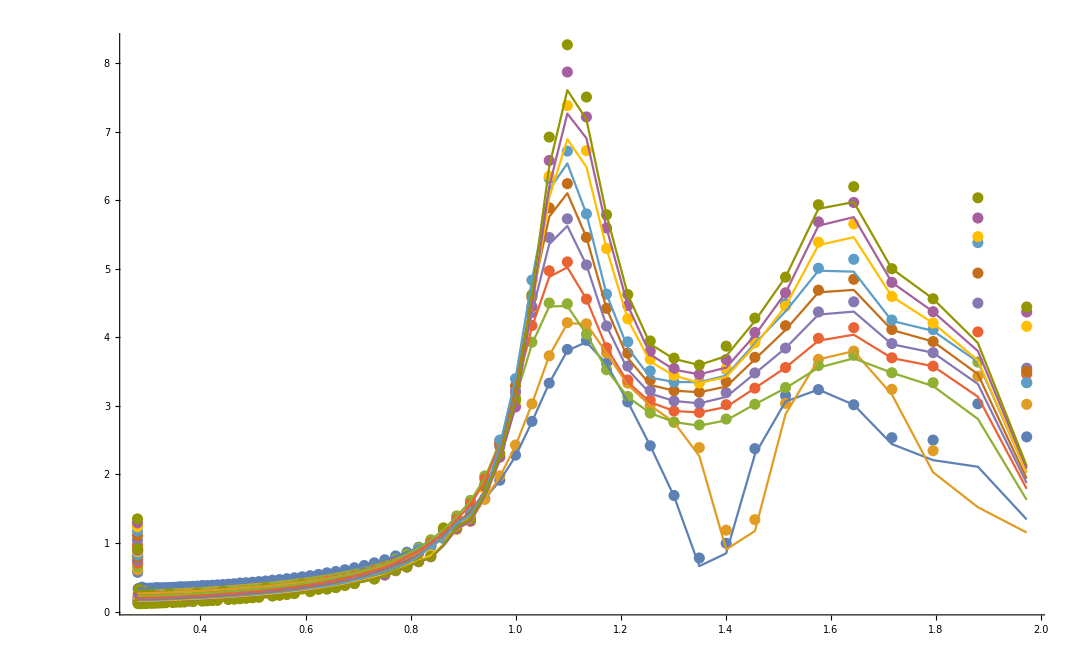

```mathematica
Show[{ListPlot[Table[Thread[{√vx[[1;;n0]] unit/1000,√(noshapeWNc[[Nci,Length[Ndata]]]["specD0q"][[1;;n0]])}],{Nci,1,Length[Nclist]}],PlotRange->All],ListLinePlot[Table[Thread[{√vx[[1;;n0]] unit/1000,Abs[noshapeWNc[[Nci,Length[Ndata]]]["ReFFD0q"]+ⅈ noshapeWNc[[Nci,Length[Ndata]]]["ImFFD0q"]][[1;;n0]]}],{Nci,1,Length[Nclist]}],PlotRange->All]},(*GridLines->{{4 140/1000,0.83},{5.9,7.7,8.9,10.2,11.3,12.6,16.1,19.5,22.4,25.6}},*)GridLines->{{4 140/1000,0.83},None},PlotRange->All]
```